```mathematica
f[x_]:=1/(1+x^2);
pts={-2,-1,0,1,2};
```

```mathematica
v=Transpose[Join[{ConstantArray[1,5]},Table[pts^i,{i,1,4}]]]
MatrixForm[v]
```

{{1,-2,4,-8,16},{1,-1,1,-1,1},{1,0,0,0,0},{1,1,1,1,1},{1,2,4,8,16}}

(1 | -2 | 4 | -8 | 16
1 | -1 | 1 | -1 | 1
1 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1
1 | 2 | 4 | 8 | 16)

```mathematica
coeff=LinearSolve[v,f[pts]]
```

{1,0,-3/5,0,1/10}

```mathematica
poly=Sum[coeff[[i]]*x^(i-1),{i,1,5}]
```

1-(3 x^2)/5+x^4/10

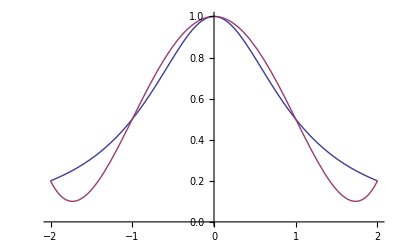

```mathematica
Plot[{f[x],poly},{x,-2,2}]
```

```mathematica
f[x_]:=1/(1+x^2);
a=-1;
b=2;
n=10;
```

```mathematica
pts=Table[a+i*(b-a)/n,{i,0,n}]
```

{-1,-7/10,-2/5,-1/10,1/5,1/2,4/5,11/10,7/5,17/10,2}

```mathematica
v=Transpose[Join[{ConstantArray[1,n+1]},Table[pts^i,{i,1,n}]]]
MatrixForm[v]
```

{{1,-1,1,-1,1,-1,1,-1,1,-1,1},{1,-7/10,49/100,-343/1000,2401/10000,-16807/100000,117649/1000000,-823543/10000000,5764801/100000000,-40353607/1000000000,282475249/10000000000},{1,-2/5,4/25,-8/125,16/625,-32/3125,64/15625,-128/78125,256/390625,-512/1953125,1024/9765625},{1,-1/10,1/100,-1/1000,1/10000,-1/100000,1/1000000,-1/10000000,1/100000000,-1/1000000000,1/10000000000},{1,1/5,1/25,1/125,1/625,1/3125,1/15625,1/78125,1/390625,1/1953125,1/9765625},{1,1/2,1/4,1/8,1/16,1/32,1/64,1/128,1/256,1/512,1/1024},{1,4/5,16/25,64/125,256/625,1024/3125,4096/15625,16384/78125,65536/390625,262144/1953125,1048576/9765625},{1,11/10,121/100,1331/1000,14641/10000,161051/100000,1771561/1000000,19487171/10000000,214358881/100000000,2357947691/1000000000,25937424601/10000000000},{1,7/5,49/25,343/125,2401/625,16807/3125,117649/15625,823543/78125,5764801/390625,40353607/1953125,282475249/9765625},{1,17/10,289/100,4913/1000,83521/10000,1419857/100000,24137569/1000000,410338673/10000000,6975757441/100000000,118587876497/1000000000,2015993900449/10000000000},{1,2,4,8,16,32,64,128,256,512,1024}}

(1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1
1 | -7/10 | 49/100 | -343/1000 | 2401/10000 | -16807/100000 | 117649/1000000 | -823543/10000000 | 5764801/100000000 | -40353607/1000000000 | 282475249/10000000000
1 | -2/5 | 4/25 | -8/125 | 16/625 | -32/3125 | 64/15625 | -128/78125 | 256/390625 | -512/1953125 | 1024/9765625
1 | -1/10 | 1/100 | -1/1000 | 1/10000 | -1/100000 | 1/1000000 | -1/10000000 | 1/100000000 | -1/1000000000 | 1/10000000000
1 | 1/5 | 1/25 | 1/125 | 1/625 | 1/3125 | 1/15625 | 1/78125 | 1/390625 | 1/1953125 | 1/9765625
1 | 1/2 | 1/4 | 1/8 | 1/16 | 1/32 | 1/64 | 1/128 | 1/256 | 1/512 | 1/1024
1 | 4/5 | 16/25 | 64/125 | 256/625 | 1024/3125 | 4096/15625 | 16384/78125 | 65536/390625 | 262144/1953125 | 1048576/9765625
1 | 11/10 | 121/100 | 1331/1000 | 14641/10000 | 161051/100000 | 1771561/1000000 | 19487171/10000000 | 214358881/100000000 | 2357947691/1000000000 | 25937424601/10000000000
1 | 7/5 | 49/25 | 343/125 | 2401/625 | 16807/3125 | 117649/15625 | 823543/78125 | 5764801/390625 | 40353607/1953125 | 282475249/9765625
1 | 17/10 | 289/100 | 4913/1000 | 83521/10000 | 1419857/100000 | 24137569/1000000 | 410338673/10000000 | 6975757441/100000000 | 118587876497/1000000000 | 2015993900449/10000000000
1 | 2 | 4 | 8 | 16 | 32 | 64 | 128 | 256 | 512 | 1024)

```mathematica
coeff=LinearSolve[v,f[pts]]
```

{16738387052921/16739950862245,-210608981121/284579164658165,-574633275856/577239684905,382234647025/17512563978964,53712287034425/56915832931633,-32565374235625/227663331726532,-4562905877375/6695980344898,1258158343750/4378140994741,11492222937500/56915832931633,-9408269062500/56915832931633,1793018125000/56915832931633}

```mathematica
poly=Sum[coeff[[i]]*x^(i-1),{i,1,n+1}]
```

16738387052921/16739950862245-(210608981121 x)/284579164658165-(574633275856 x^2)/577239684905+(382234647025 x^3)/17512563978964+(53712287034425 x^4)/56915832931633-(32565374235625 x^5)/227663331726532-(4562905877375 x^6)/6695980344898+(1258158343750 x^7)/4378140994741+(11492222937500 x^8)/56915832931633-(9408269062500 x^9)/56915832931633+(1793018125000 x^10)/56915832931633

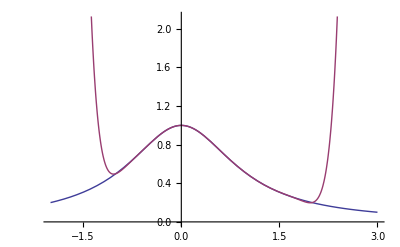

```mathematica
Plot[{f[x],poly},{x,a-1,b+1}]
```